## Repelling curves in the HES T -> T T string amplitudes

This notebook  contains all the relevant code for the paper Multidimensional chaos II: String scattering amplitudes, curve repulsion, and random matrices

## Computing the amplitude and curves

In this first part we define all the functions that we need to compute and plot the amplitude and the curves where its derivatives vanish.

### Definitions

#### Definitions: The HT->TT amplitude

Below are the main expressions for the function that we will investigate. The dressing factor in the HES T -> T T scattering amplitude, taken in the high-energy fixed-angle limit.

```mathematica
(* The amplitude in the high-energy fixed angle limit, where s >> Subscript[M, n]^2, is given in terms of the following Jacobi polynomials *)

Clear[pn]
pn[n_,x_:x,y_:y]:=JacobiP[n-1,-2n+1,-n √(1-x^2)y,(x-3)/(x+1)];
(* p0 is the common prefactor for all n*)
p0[x_:x,y_:y] = (√(1-x^2)√(1-y^2))/(1+x);
pn[0,x_,y_]:=p0[x,y]
```

```mathematica
(* For a general partition, the amplitude is: *)
AHTTT[gn_,x_:x,y_:y]:=Block[{JJ=Total[gn]},
((√(1-x^2)√(1-y^2))/(1+x))^JJ Product[pn[n,x,y]^gn[[n]],{n,1,Length@gn}]
];
(* In the notation of the paper this is DHTTT, i.e. the dressing factor. The full amplitude is this times the Veneziano amplitude *)
```

#### Useful functions for integer partitions

```mathematica
(* Load Mathematica's Combinatorica package for the function RandomPartition[n] : *)
Needs["Combinatorica`"]
```

In general, we can represent partitions in one of two ways: as a set of the summands n that go into the partition, or by the “population numbers” gn. For example, the partition 12 = 4 + 4  + 2 + 1 + 1 is represented either as
prt = {4,4,2,1,1}
or as
gn = {2,1,0,2}

```mathematica
(* Definition of the conjugate partition *)
ConjugatePartition[prt_] :=
    Select[Table[Length @ Select[prt, # >= i&], {i, 1, Total @ prt}],
         # > 0&];
```

```mathematica
(* PNM[N,m] = number of partitions of N of length m, calculated using generating function. PNM[N] = list of all PNM *)
Clear[PNM]
PNM[n_] := PNM[n] =
    Module[{pnm},
        pnm = Table[SeriesCoefficient[Product[1 / (1 - x^k), {k, 1, m
            }], {x, 0, n}], {m, 1, n}];
        pnm = Differences[pnm];
        Return[Flatten @ PrependTo[pnm, {1}]]
    ];
    
    
PNM[n_, m_] := PNM[n, m] =
    SeriesCoefficient[Product[1 / (1 - x^k), {k, 1, m}], {x, 0, n}] -
         SeriesCoefficient[Product[1 / (1 - x^k), {k, 1, m - 1}], {x, 0, n}];
```

```mathematica
(* Geometric distribution of {g_n}, needed for the algorithm *)
distZm[NN_, n_] :=
    GeometricDistribution[(1 - Exp[-((n π) / Sqrt[6 NN])])];
    
(* Probabilistic algorithm to generate partition of N with maximum n_max.
Can specify if maximum is fixed to Subscript[n, max] by setting third argument to True, or only ≤ Subscript[n, nmax] (default behavior) *)
RandomPartitionMaxN[Nn_, nmax_,fixedNmax_:False] :=
    Module[{prt, i, zms, ms = Range[2, nmax], u, k = -1},
       While[
            Or[k < 0, (u = RandomReal[]) >= Exp[(-k π) / Sqrt[6 Nn]]]
                
            ,
            zms = Table[RandomVariate[distZm[Nn, i]], {i, 2, nmax}];
            If[fixedNmax, zms[[nmax - 1]] = zms[[nmax - 1]] + 1];
            k = Nn - Total @ (ms zms);
        ];
        zms = Flatten[{k, zms}];
        prt = {};
        Do[prt = Join[prt, ConstantArray[i, zms[[i]]]];, {i, 1, nmax}];
        Return @ prt
    ];

(* Probabilistic algorithm to generate partition of N of length J. 
Take a partition with fixed Subscript[n, max] = J, and return its conjugate *)
RandomPartitionJ[Nn_, jj_] := ConjugatePartition[RandomPartitionMaxN[Nn,jj,True]]
```

```mathematica
(* Sets values of gn, NN, and JJ, given a partition prt *)
(* Also defines ns = set of unique n in the partition *)
findgn[prt_]:= Module[{},
	gn = Table[Count[prt,i],{i,1,Max[prt]}];
	NN = Total[prt];
	JJ = Length[prt];
	ns = DeleteCases[DeleteDuplicates[prt],1];
	gn
	];
```

#### Spacing statistics: functions for analysis and plotting

```mathematica
(* The probability distribution functions of spacings and ratios in the Gaussian β ensemble *)
(* Valid for any β > 0 *)

(* Distribution of spacings :*)
distβδ[β_]:=ProbabilityDistribution[2 ⅇ^(-(s^2 Gamma[(2+β)/2]^2)/Gamma[(1+β)/2]^2) s^β Gamma[(1+β)/2]^(-2-β) Gamma[(2+β)/2]^(1+β),{s,0,∞}];


(* Distribution of the normalized level spacings r̃ *)
distβT[β_]:=ProbabilityDistribution[2 (3^((3 (1+β))/2) (x+x^2)^β (1+x+x^2)^(-1-(3 β)/2) Gamma[1+β/2]^2)/(2 π Gamma[1+β]),{x,0,1}];
```

```mathematica
(* Compute spacing ratios from spacings *)
rδ[δ_]:=δ[[2;;All]]/δ[[1;;Length[δ]-1]];

(* Compute the normalized spacing ratios r̃∈[0,1] *)
rT[r_?NumberQ]:=Min[r,1/r];
rT[r_?ListQ]:=rT/@r;
```

```mathematica
Clear[plotRnTilde];
(* Given a set of Subscript[r, n] (where each element in the set is a list containing all the values for a particular state),
fits the distribution of Subscript[r̃, n] to the β ensemble, an plots the histogram *)
plotRnTilde[rn_:rn,label_:""] := Module[{rx=rn,rt,β},
	rt = rT[Flatten@rx];

	hist = Histogram[rt,{0,1,1/40},"PDF"
		,PlotRange->{{0,1.00},{0,2.3}}
		,AxesLabel->{"(r̃)_n","PDF"}
		,ImageSize->800
		,AxesStyle->Directive[FontSize-> 24]
		,LabelStyle->Directive[FontSize-> 24]
		,PlotLabel->label
		];
	
	distRMT=EstimatedDistribution[rt,distβT[β],{β,1.7}];
	
	pdfRMT=PDF[distRMT,r];
	pdfGOET = PDF[distβT[1],r];
	pdfGUET = PDF[distβT[2],r];

	pl = Plot[{pdfRMT,pdfGUET,pdfGOET},{r,0,1}
		,PlotStyle->{{Black,Thick},{Red,Thick,Dashed},{Blue,Thick,Dashed}}
		,PlotRange->Full
		,PlotLegends->Placed[{StringJoin["β = ",ToString@Round[distRMT[[1,2,2]],0.001]],"GUE","GOE"},{Left,0.8}]
		,Epilog->Placed[{StringJoin["β = ",ToString@Round[distRMT[[1,2,2]],0.001]],"GUE","GOE"},{Right,0.8}]
		,LabelStyle->Directive[FontSize-> 22]
	];
	
	βfit=distRMT[[1,2,2]];

	pltR = Show[hist, pl,Epilog->Inset[Style[StringJoin["<r̃> = ",ToString@Round[Mean@rt,0.001]],FontSize->24],{0.9,2.2},{0.9,2.2}]]
];
```

#### General and auxiliary definitions

```mathematica
(* Assumptions to simplify expressions *)
$Assumptions={n≥1,n ∈Integers,-1≤x≤1,-1≤y≤1};
```

```mathematica
(* Default style for figure *)

figure[label_:None]:= plt = Plot[{},{x,-1,1},PlotRange->plr,Frame->True,LabelStyle->Directive[FontSize->28],FrameLabel->{"Cos[θ]","Cos[ϕ]"},AspectRatio->1,ImageSize->640,PlotLabel->label];

show[fig_]:= Show[plt,fig];

(* Default plot range *)
plr={{-0.99,0.99},{-0.99,0.99}};
```

```mathematica
(* Collect terms in y *)
colly[exp_]:=Collect[exp,y,Simplify];
collz[exp_]:=Collect[exp,z,Simplify];
```

```mathematica
(* Time-keeping function to keep track of running computations *)
beep[]:=WriteString["stdout","*"];

(* MATLAB style tic[] toc[] functions *)
tic[] := tictime = AbsoluteTime[];
toc[] := Print["Elapsed time: ", AbsoluteTime[] - tictime, " seconds. Current time = ",DateString[]];

now[]:= Print["Current time = ",DateString[]];
```

```mathematica
(* Normalize a vector to have mean 1 *)
norm[v_]:=v/Mean[Flatten[v]];
```

```mathematica
(* array of zeros *)
Zeros[n_?IntegerQ]:= ConstantArray[0,n];
Zeros[l_?ListQ]:= Zeros[Length@l];
```

```mathematica
(* Normalizes a vector of length L such that its mean spacing becomes 1 *)
normL[v_]:=v/(Max[v]-Min[v])(Length[v]-1);
```

```mathematica
(* clamp function to restrict a real number to be in the range [-1,1] (or specify manually other limits *)
Clear[clamp]
clamp[v_?NumberQ,vmin_:-1,vmax_:1]:=Min[Max[v,vmin],vmax];
clamp[vmin_,vmax_][v_]:=clamp[v,vmin,vmax]
clamp[v_?ListQ]:=clamp/@v;
```

### Initialization: precompute polynomials and their derivatives

To speed up operations, we compute the polynomials P_n that enter the HTTT amplitude, up to a value n_max,
as well as their x and y derivatives.
In practice we will use mostly these functions, rather than AHTTT defined above.

```mathematica
poly[n_]:=poly[n] = (pn[n,x,z/(√(1-x^2))]//collz)/.z->√(1-x^2)y;
poly[0]=p0[x,y];
```

```mathematica
nmax = 30;

Do[poly[n];beep[];,{n,1,nmax}]
```

******************************

```mathematica
dxpoly[n_]:=dxpoly[n] = D[poly[n],x]//colly;
dypoly[n_]:=dypoly[n] = D[poly[n],y]//colly;
```

```mathematica
Do[dxpoly[n]; dypoly[n]; beep[];
,{n,1,nmax}]
```

******************************

```mathematica
(* Turn off the following error message from Solve:
"Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result."
*)
Off[Solve::ratnz]
```

#### Spectral form factor: predictions of RMT

```mathematica
(* Prediction of the connected part of the SFF (ramp -> plateau) for β *)

(* This formula is our conjecture of the interpolation from GOE to GUE based on the fits that we have found for different values of β∈(1,2): *)
predβ1[β_][τ_]:=Piecewise[{{2/β τ -(2/β-1)τ Log[1+ 2τ],τ<1},{2/β-(2/β-1)τ Log[(2τ+1)/(2τ-1)],τ>=1}}];

(* The interpolation from GUE to GSE doesn't work for τ near 1. I also couldn't find the formula for 1<=τ<2 *)
predβ2[β_][τ_]:=Piecewise[{{2/β τ+1/2(2/β-1)τ Log[Abs[1-τ]],τ≤0.985},{Null,True}}]

predβ[β_][τ_]:=If[β<=2,predβ1[β][τ],predβ2[β][τ]];
```

```mathematica
(* Realization of Circular Beta ensemble, algorithm due to Killip-Nenciu *)

Clear[distNu,randomTheta];
distNu[ν_]:=BetaDistribution[1,1+(ν-3)/2];
randomTheta[ν_]:=Block[{dr,r,θ},
dr=distNu[ν];
r=√RandomVariate[dr];
θ=RandomReal[{0,2π}];
Return[r Exp[ⅈ θ]];
];
randomTheta[1]:=Exp[2π ⅈ RandomReal[]];

(* Killip-Nenciu construction for circular Beta ensemble *)
Clear[RandomCBEMatrix];
RandomCBEMatrix[n_,β_]:=Module[{m,α,ρ,X,x,me,mo,k},
me=DiagonalMatrix@Table[Subscript[x, k],{k,0,n-1,2}];
mo=DiagonalMatrix@Table[Subscript[x, k],{k,-1,n-1,2}];
Do[
Subscript[α, k]=randomTheta[1+β(n-k-1)];
Subscript[ρ, k]=√(1-Abs[Subscript[α, k]]^2);
,
{k,0,n-2}
];
Subscript[α, n-1]=randomTheta[1];
Subscript[ρ, n-1]=0;
Subscript[X, -1]=1;
mo=mo/.Subscript[x, -1]->Subscript[X, -1];
Do[
Subscript[X, k]=({{Subscript[α, k]*, Subscript[ρ, k]}, {Subscript[ρ, k], -Subscript[α, k]}});
me=me/.Subscript[x, k]->Subscript[X, k];
mo=mo/.Subscript[x, k]->Subscript[X, k];
,
{k,0,n-2}
];
Subscript[X, n-1]=Subscript[α, n-1]*;
mo=mo/.Subscript[x, n-1]->Subscript[X, n-1];
me=me/.Subscript[x, n-1]->Subscript[X, n-1];

mo=ArrayFlatten@mo;
me=ArrayFlatten@me;

Return[me.mo]
];

eigenvaluesBeta[nn_,β_]:= Block[{λ,m},
	m = RandomCBEMatrix[nn,β];
	λ = Eigenvalues[m];
	normL[Sort[Arg[λ]]]
	];
```

### Plotting the amplitude and its curves for low N

#### Analytic expressions: single harmonic at N = 2 or 3

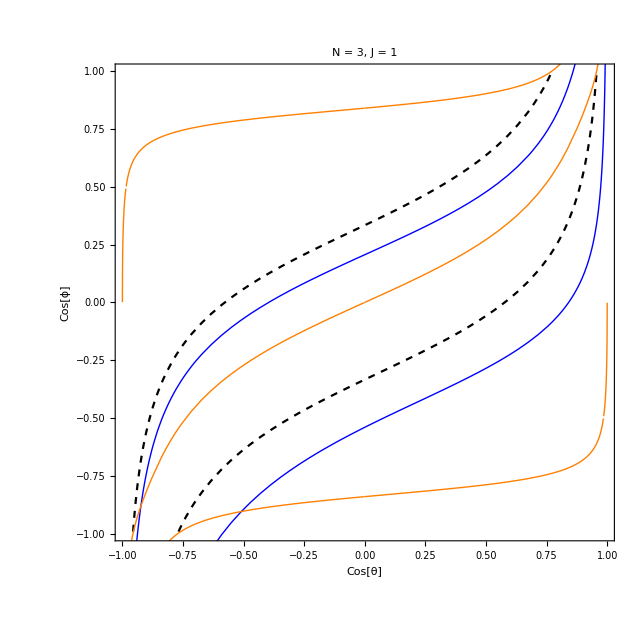

```mathematica
(* Here we find and plot the analytic expressions for the curves of zeros of the ampitude at very low N, i.e. N = 2 or 3 *)
prt = {2};
prt = {3};
findgn[prt];

a = AHTTT@gn//colly;
d1=D[a,x]//colly;
d2=D[a,y]//colly;

l1=((1-x^2)d1)/p0[]^JJ//Simplify//colly;
l2=((1-y^2)d2)/p0[]^JJ//Simplify//colly;

za = y/.Solve[pn[NN]==0,y];
zd1=y/.Solve[l1==0,y];
zd2=y/.Solve[l2==0,y];

figure[StringJoin["N = ",ToString[NN],", J = 1"]];
Show[plt,Plot[za,{x,-1,1},PlotStyle->{{Black,Dashed}},PlotRange->plr,Frame->True],Plot[Re@zd1,{x,-1,1},PlotStyle->{{Blue,Thick}}],Plot[Re@zd2,{x,-1,1},PlotStyle->{{Orange,Thick}}]]
```

```mathematica
(* Here we generate also the contour plot (also use for small N) *)
xs=Range[-0.99,0.99,0.005];

(* Help Mathematica produce a clean plot by specifying a minimal value of Log[Abs[A]] to be plotted *)
vmin=-6;
num[x_?NumberQ]:=x;
num[x_]:=vmin;

dat=Table[num[clamp[Re[Log[Abs[a]]],vmin,6]/.{x->x0,y->y0}],{x0,xs},{y0,xs}];

figure[StringJoin["N = ",ToString[NN],", J = 1"]];
ListContourPlot[Transpose@dat,Contours->24,ContourStyle->None,ColorFunction->"DeepSeaColors",DataRange->plr]//show
```

-Graphics-

### Plots and verifications for a single partition

#### Zeros of the amplitude

```mathematica
Clear[qn,yofx];

(* Solve for zeros of each polynomial separately *)
qn[n_]:=qn[n]=(1+x)^(n-1)poly[n]//colly
yofx[n_][x0_]:=y/.Solve[(qn[n]/.x->x0)==0,y]

(* Compute the curves of zeros for each n and save them *)
Clear[fz]
fz[1]:={};
fz[n_]:=fz[n]=Module[{xs=Range[-999/1000,999/1000,5/1000],fs,ys}
,
ys = yofx[n]/@xs;
ys = Re[N[ys]];
ys = Sort/@ys;
ys = Transpose@ys;

fs = Interpolation[Transpose@{N[xs],#},InterpolationOrder->5]&/@ys
];
```

```mathematica
(* Can compute all curves of zeros in advance *)
Do[qn[n];fz[n]; beep[];,
{n,1,nmax}
];
```

****************************

$Aborted

{1,1,1,2,2,2,3,3,4,10,21}

{3,3,2,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1}

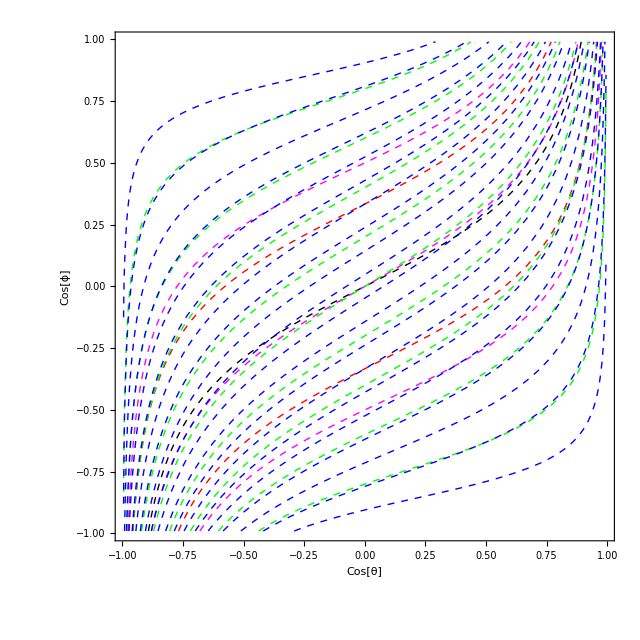

```mathematica
(* Plot curve of all zeros for a given partition *)
prt=RandomPartitionMaxN[50,nmax]

findgn@prt
fz/@ns;

(* Produce plot of curves where the amplitude is zero, with different colors for the zeros of each harmonic *)
colors = {Black,Red,Magenta,Green,Blue,Orange};
figure[];
Show[
plt,
Table[
Plot[Through[Flatten[fz[ns[[i]]]][x]],{x,-0.995,0.995},PlotStyle->{{colors[[Mod[i,6]]],Dashed,Thin}},PlotRange->plr]
,{i,1,Length@ns}
]
]
```

#### Plot curves of zeros of derivative for a given partition

```mathematica
(* Define a state *)
NN = 20;

prt = RandomPartitionMaxN[NN,nmax]

findgn@prt;
```

{1,1,1,1,2,4,10}

```mathematica
(* Curves of zeros can be plotted already *)
fs=fz/@ns;
fs=Flatten@fs;
fs = SortBy[fs,#[0.1]&];
fsx=Table[fs[[i]][x],{i,1,Length@fs}];
fsx = SortBy[fsx,#/.x->0.1&];
```

```mathematica
(* The two log-derivatives are given by *)
d1n =-(JJ/2)/(1-x)-(NN-JJ/2)/(1+x)+Plus@@Table[gn[[n]] dxpoly[n]/poly[n],{n,ns}];

d2n =-(JJ/2)/(1-y)-(-JJ/2)/(1+y)+Plus@@Table[gn[[n]] dypoly[n]/poly[n],{n,ns}];
```

```mathematica
(* Compute zeros of d/dx and d/dy numerically *)
Clear[ytx,ypx]
ytx[x0_]:=Sort[y/.Solve[(d1n/.x->x0)==0,y]]
ypx[x0_]:=Sort[y/.Solve[(d2n/.x->x0)==0,y]]

(* Then calculate at discrete points and then use interpolation to define the curves *)
dx=5/1000;
xs=Range[-999/1000,999/1000,dx];

Print["Starting!"]

yts =ytx/@xs//N//Re;
yts = Sort/@yts;
yts = Transpose@yts;
Print["Computed yts!"]

yps = ypx/@xs//N//Re;
yps = Sort/@yps;
yps = Transpose@yps;
Print["Computed yps!"]
```

Starting!

Computed yts!

Computed yps!

```mathematica
fts = Interpolation[Transpose@{xs,#},InterpolationOrder->5]&/@(clamp[yts]);
ftsx=Table[fts[[i]][x],{i,1,Length@fts}];
Print["Computed ftsx!"]

fps = Interpolation[Transpose@{xs,#},InterpolationOrder->5]&/@(clamp[yps]);
fpsx=Table[fps[[i]][x],{i,1,Length@fps}];
Print["Computed fpsx!"]

Print["Done!"]
```

Computed ftsx!

Computed fpsx!

Done!

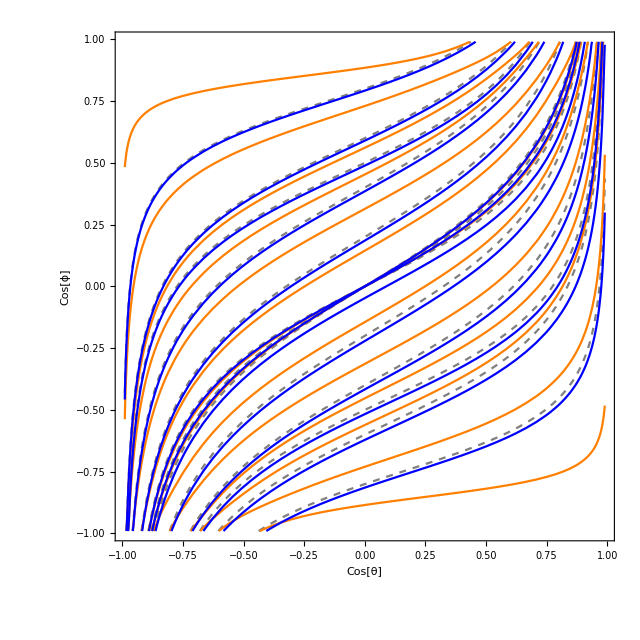

```mathematica
(* And plot the curves *)
figure[];
pl0=Plot[fsx,{x,-0.99,0.99},PlotStyle->{{Gray,Dashed}},PlotRange->plr];
pl1=Plot[fpsx,{x,-0.99,0.99},PlotStyle->{Orange},PlotRange->plr];
pl2=Plot[ftsx,{x,-0.99,0.99},PlotStyle->{Blue},PlotRange->plr];
Show[plt,pl0,pl1,pl2,PlotRange->plr]
```

### Gathering data from many partitions

This is where the main computation is taking place. We generate a list of random partitions of a fixed N, and compute the curves for each. The results are saved in a DAT file that can be re-imported for the later analysis.

#### Choose partitions and initialize variables

```mathematica
NN = 100;
NP = 100;

prts = Table[RandomPartitionMaxN[NN,nmax],NP];


resume = 1;
dx=5/1000 ;
xs=Range[-999/1000,999/1000,dx];

yt = {};
yp = {};
```

#### Loop for computing curves

```mathematica
(* Can comment out timing functions if not needed *)
now[];
tic[];

Do[
(* For each partition *)
prt = prts[[ii]];

findgn@prt;

(* We define the log derivatives *)
d1n =-(JJ/2)/(1-x)-(NN-JJ/2)/(1+x)+Plus@@Table[gn[[n]] dxpoly[n]/poly[n],{n,ns}];

d2n =-(JJ/2)/(1-y)-(-JJ/2)/(1+y)+Plus@@Table[gn[[n]] dypoly[n]/poly[n],{n,ns}];

(* To find the curves where the derivative is zero we need only the numerator, which we simplify here *)

d1n = d1n//Together//Numerator//colly;
d2n = d2n//Together // Numerator//colly;

(*beep[];*)
(*toc[];*)

(* Compute zeros of d/dx and d/dy numerically.
First define the solver functions at fixed x *)
Clear[ytx,ypx];
ytx[x0_]:=y/.Solve[(d1n/.x->x0)==0,y];
ypx[x0_]:=y/.Solve[(d2n/.x->x0)==0,y];

(* Then calculate at discrete points *)
(* Note: the computation first solves the polynomial equations with exact coefficients, and then converts the results to finite machine precision numbers by N[] 
This avoids numerical errors in the stage of solving the equations, since polynomial equations can be highly sensitive to small changes in the coefficients at high degree.
Once we have the solution for y, we do not need the infinite precision anymore, as machine precision is more than enough for our curves.
*)
yts = (ytx/@xs)//N;
yps = (ypx/@xs)//N;

(* Dismiss a small imaginary part, which is always a numerical artifact [as can be verified] *)
yts = Re[yts];
yps = Re[yps];

(* Transpose and sort to get each array in yts to be a continuous curve *)
yts =Transpose@(Sort/@yts);
yps =Transpose@(Sort/@yps);

AppendTo[yt,yts];
AppendTo[yp,yps];
resume = resume + 1;

beep[];
toc[]; tic[];

(* Save temporary results to prevent data loss in case of crash *) 
If[Divisible[resume,4],Save[StringJoin["HTTT-2D-resume-",ToString[NN],"-",StringReplace[DateString["ISODateTime"],":"->"-"],".dat"],{prts,xs,yt,yp,resume}]];
,
{ii,resume,Length@prts}
];
resume
```

```mathematica
Save[StringJoin["HTTT-2D-resume-",ToString[NN],"-",StringReplace[DateString["ISODateTime"],":"->"-"],".dat"],{prts,xs,yt,yp,resume}]
resume
```

```mathematica
(* Load data file to resume interrupted calculation *)
Get["HTTT-2D-resume-60.dat"]
Length@yt
resume
```

## Analyzing the curves and their spacings

### Load data

```mathematica
(* After computing using code above, the dat file should contain the list of partitions,
and the two curves Subscript[y, θ](x) and Subscript[y, ϕ](x), represented as the discrete set of xs, yt(xs), yp(xs) *)
Get["HTTT-curves-100.dat"]
NN = Total[prts[[1]]]
Length@yt
```

101

100

100

### Areas: their ratios and SFF

#### Compute the areas

```mathematica
(* Compute areas *)
At={};
Ap = {};

(* We define the curves by interpolating between the 400 points that we computed for each curve, so we have a smooth curve we can NIntegrate over to get the areas .
This can potentially introduce some numerical error, but we can check the dependence
 on this interpolation order parameter to see that results are not sensitive to its value *)
intOrd = 5;
Do[
yps=Re[yp[[ii]]];
yps = clamp[yps];
If[Not[ListQ[yps]],Break[]];

fps = Interpolation[Transpose@{xs,#},InterpolationOrder->intOrd]&/@yps;
fpsx = Through[fps[x]];

An=NIntegrate[fpsx,{x,-0.99,0.99}]+2;
AppendTo[Ap,An];

yts=Re[yt[[ii]]];
yts = clamp[yts];
If[Not[ListQ[yts]],Break[]];

fts = Interpolation[Transpose@{xs,#},InterpolationOrder->intOrd]&/@yts;
ftsx = Through[fts[x]];

An=NIntegrate[ftsx,{x,-0.99,0.99}]+2;
AppendTo[At,An];

beep[];
,
{ii,1,Length@yp}
];
```

****************************************************************************************************

#### Distribution of spacing ratios and fit

N = 100 (y-derivate)

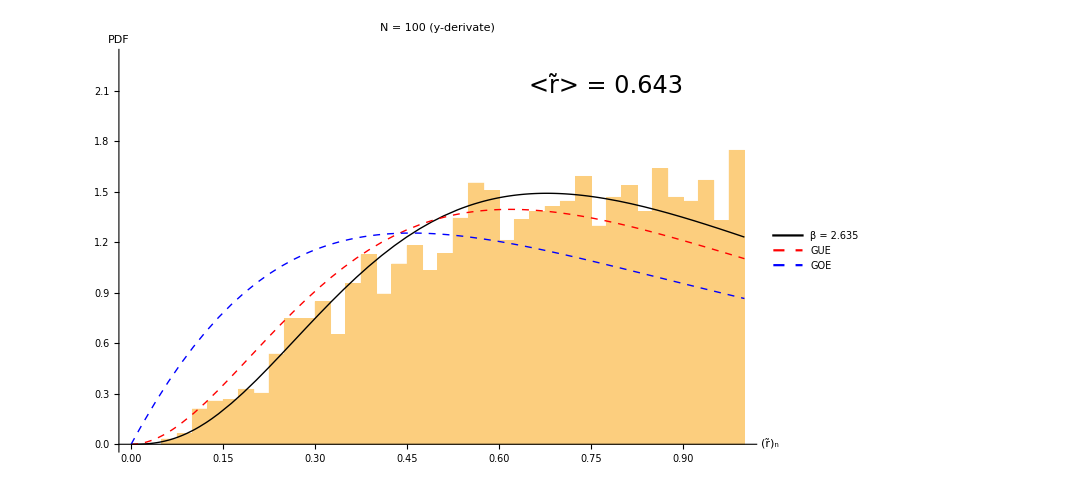

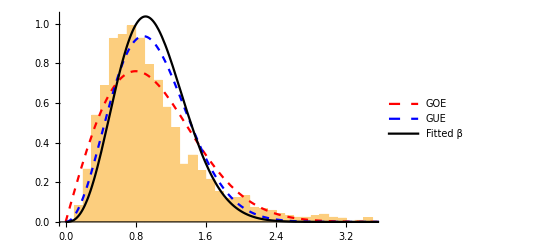

```mathematica
(* Pick Ap or At *)
torp = "p";

As = If[torp=="t",At,Ap];
label = StringJoin["N = ",ToString[NN]," (",If[torp=="t","x","y"],"-derivate)"]

δs = (Differences/@As)//norm;
rs = rδ/@δs;

plt=plotRnTilde[Flatten@rs,label]

pdf = PDF[distβδ[βfit],s];

Show[Histogram[Flatten[δs],{0,3.5,0.1},"PDF"],Plot[{π/2 s Exp[-π/4 s^2],32/π^2 s^2 Exp[-4/π s^2],pdf},{s,0,4},PlotLegends->{"GOE","GUE","Fitted β"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}}]]
```

#### SFF: Plot on log-log scale

```mathematica
(* The Ap eigenvalues are symmetric under A -> 4-A, so we remove the symmetry before computing the SFF *)
λs = If[torp=="t",At,Ap = Select[#,(#<2&)]&/@Ap];
λs=normL/@λs;
```

```mathematica
(* Init SFF calculation *)
dt=1./200;
τs=10^Range[-2,2,dt];
data=Zeros[τs];
resume=1;
```

****************************************************************************************************

101

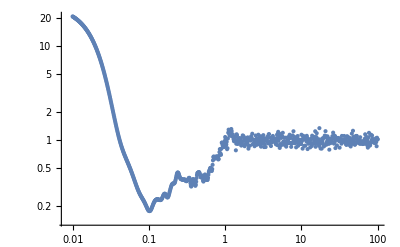

```mathematica
Do[
λ=λs[[ii]];
nn = Length@λ;
Clear[sff];
sff[τ_]:=1/nn Abs[Total[Exp[ⅈ λ 2π τ]]]^2;
data=data+sff/@τs;

beep[];
resume=resume+1;
,
{ii,resume,Min[2000,Length@λs]}]
resume
ListLogLogPlot[Transpose@{τs,Re@(data/resume)},Joined->False]
```

101

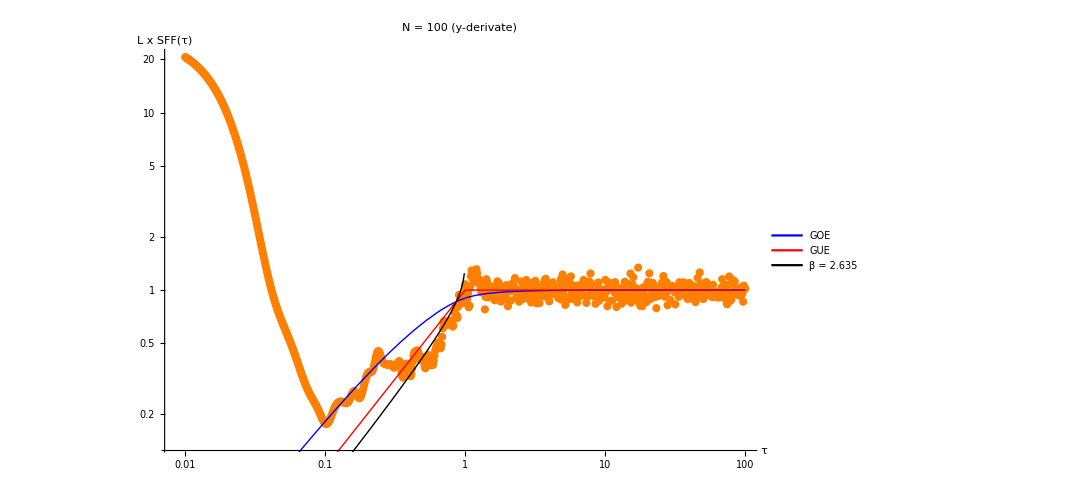

```mathematica
ns=Min[2000,resume]
d0=Transpose@{τs,data/ns};

d1=Re@d0;

plt=Show[
ListLogLogPlot[d1,ImageSize->Large,PlotRange->{Full,Full},PlotLabel->label,AxesLabel->{"τ","L x SFF(τ)"},PlotStyle->{Orange},Joined->False]

,LogLogPlot[{predβ[1][τ],predβ[2][τ],predβ[βfit][τ]},{τ,Min[τs],Max[τs]},PlotStyle->{{Blue,Thick},{Red,Thick},{Black,Thick}},PlotRange->Full,PlotLegends->Placed[{"GOE","GUE",StringJoin["β = ",ToString@Round[βfit,0.001]]},{Right,0.2}],LabelStyle->Directive[FontSize-> 22]]


,ImageSize->800,AxesStyle->Directive[FontSize-> 22]
		,LabelStyle->Directive[FontSize-> 22]


]
```

#### SFF: Plot on linear scale (with subtraction of disconnected part)

To do: check if the averaging works well with GOE/GUE spectra with different sizes L!

```mathematica
(* The Ap eigenvalues are symmetric under A -> 4-A, so we remove the symmetry before computing the SFF *)
λs = If[torp=="t",At,Ap = Select[#,(#<2&)]&/@Ap];
λs=normL/@λs;
```

```mathematica
(* Init SFF calculation *)
dt=1./200;
τs=Range[dt,2,dt];
data=Zeros[τs];
data2=Zeros[τs];
resume=1;
```

********************************************************************************************************************************************************************************************************

2001

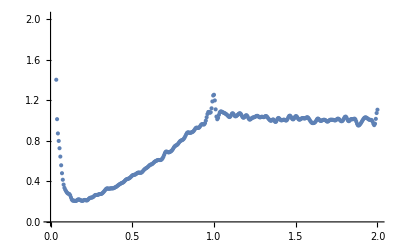

2000

```mathematica
Do[
λ=λs[[ii]];
nn = Length@λ;
Clear[sff];
sff[τ_]:=1/nn Abs[Total[Exp[ⅈ λ 2 π τ]]]^2;
char[τ_]:=√(1/nn)Total[Exp[ⅈ λ 2 π τ]]; (* Normalize with square-root because later it is squared again *)
data=data+sff/@τs;
data2 = data2 +char/@τs;

If[Divisible[resume,10],beep[]];
resume=resume+1;
,
{ii,resume,Min[2000,Length@λs]}]
resume
ListPlot[Transpose@{τs,Re@(data/resume)},Joined->False]

ns=Min[2000,resume-1]
d0=Transpose@{τs,Re[data/ns]-Abs[data2/ns]^2};
```

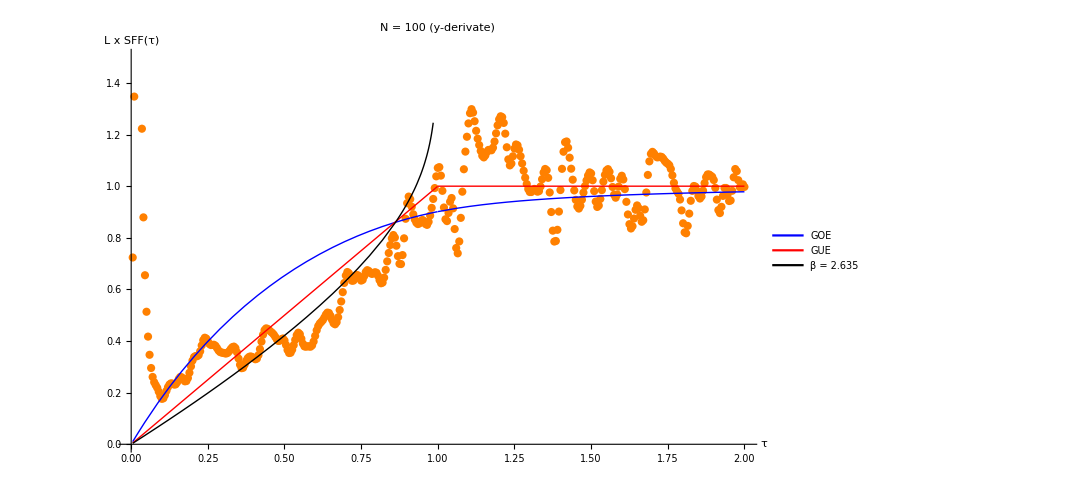

```mathematica
plt=Show[
ListPlot[d0,ImageSize->Large,PlotRange->{{0,2},{0,1.5}},PlotLabel->label,AxesLabel->{"τ","L x SFF(τ)"},PlotStyle->{Orange},Joined->False]

,Plot[{predβ[1][τ],predβ[2][τ],predβ[βfit][τ]},{τ,Min[τs],Max[τs]},PlotStyle->{{Blue,Thick},{Red,Thick},{Black,Thick}},PlotRange->Full,PlotLegends->Placed[{"GOE","GUE",StringJoin["β = ",ToString@Round[βfit,0.001]]},{Right,0.2}],LabelStyle->Directive[FontSize-> 22]]

,ImageSize->800,AxesStyle->Directive[FontSize-> 22]
		,LabelStyle->Directive[FontSize-> 22]


]
```

#### Test: Random matrices

Here we check the effect of the ensemble averaging we performed to compute the SFF for the HTTT results, by doing the same for RMT spectra.
We can use the circular ensembles since their spectra do not require unfolding.

```mathematica
(* Take the same "distribution of lengths" as in the data set *)
ls = Length/@If[torp=="t",At,Select[#,(#<2&)]&/@Ap]
(* But with 10 times the matrices *)
ls = Flatten[Table[ls,20]];

λbs = {};
```

{25,34,16,25,13,27,22,30,28,22,19,14,15,38,22,33,27,45,28,26,32,14,24,39,30,24,32,37,29,26,25,25,39,22,27,14,36,28,31,20,38,27,22,45,30,23,42,26,28,21,31,39,32,20,24,19,31,25,21,29,23,22,29,34,22,31,29,21,20,17,25,36,17,32,26,36,18,35,14,21,23,27,27,19,20,31,37,28,23,21,23,31,35,22,31,24,27,31,25,26}

```mathematica
Do[
nn = ls[[i]];
AppendTo[λbs,eigenvaluesBeta[nn,βfit]];
If[Divisible[i,10],beep[]];
,
{i,1,Length[ls]-Length@λbs}
];

δs=Differences/@λbs;
rs = rδ/@δs;
(*
(* Check the distribution of rn *)
plotRnTilde[rs]
*)
(* After generating the spectrum, can compute the SFF using above code. We can see that there are some effects due to the varying lengths. For example, the subtraction of the disconnected part doesn't completely work, even though it works perfectly with fixed length. *)
λs = λbs;
Length[λs]
```

********************************************************************************************************************************************************************************************************

2000

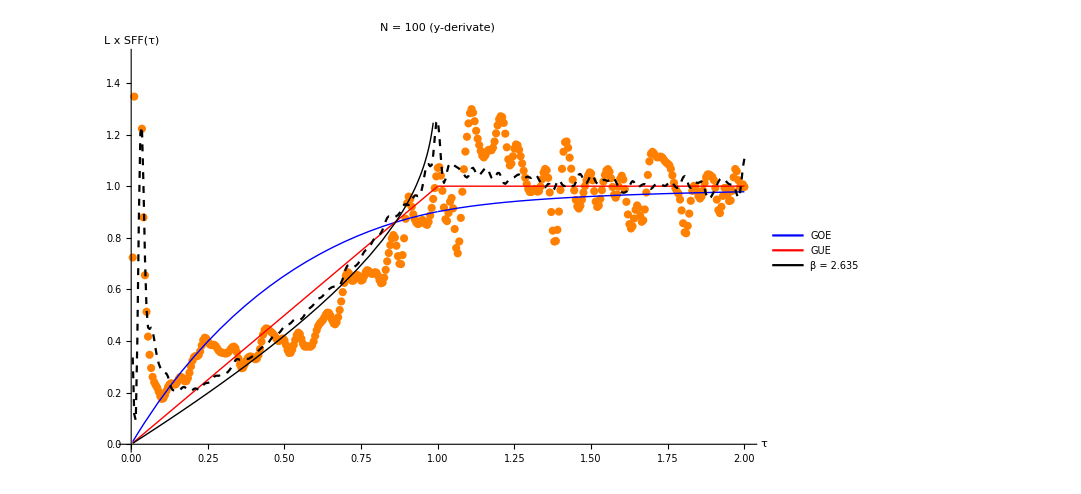

```mathematica
Show[plt,ListPlot[d0,PlotStyle->{{Black,Dashed}},Joined->True]]
```